# TuringMachine

## Number of Rules

```mathematica
NumRules[s_,k_]:=(2 s k)^(s k);(*Number of rules for s states,k colors*)
```

```mathematica
NumRules[2,3]
```

2985984

## Converting rules

```mathematica
NumberToRuleset[{ruleno_,states_,colors_}] := Flatten @ 
	MapIndexed[
		{1,-1} #2+{0,colors} -> {1,1,2} Mod[Quotient[#1,{2 colors,2,1}],{states,colors,2}]+{1,0,-1}&,
		Partition[IntegerDigits[ruleno,2 states colors,states colors],colors],
		{2}
	];
```

```mathematica
RulesetToNumber[{rules_,states_,colors_}] := 
	FromDigits[
		Function[{s,k,dx},2*colors*(s-1)+2k+(dx/.-1->0)] @@@ ($x=ReplaceAll[
			Tuples[{Range[states],colors-Range[colors]}], 
			Append[rules,{x_,y_} :> {x,y,-1}]
		]),
		2*states*colors
	];
```

### convert the 2,3 UTM number to a rule list

```mathematica
NumberToRuleset[{596440,2,3}]
```

{{1,2}→{1,1,-1},{1,1}→{1,2,-1},{1,0}→{2,1,1},{2,2}→{1,0,1},{2,1}→{2,2,1},{2,0}→{1,2,-1}}

### convert the rule list back to a number -- it’s the same as we started with

```mathematica
num=RulesetToNumber[{{{1,2}->{1,1,-1},{1,1}->{1,2,-1},{1,0}->{2,1,1},{2,2}->{1,0,1},{2,1}->{2,2,1},{2,0}->{1,2,-1}},2,3}]
DrawRule[{num,2,3}]
```

596440

-Graphics-

### design a machine that oscilattes backwards and forwards

```mathematica
num=RulesetToNumber[{{{1,0}->{2,0,-1},{2,0}->{1,0,1}},2,3}];
DrawRule[{num,2,3}]
```

-Graphics-

### simulate it

```mathematica
TuringMachine[{num,2,3},{1,{{},0}},20][[All,1,2]]
```

{2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2}

## Drawing rules

```mathematica
DrawRule[{ruleno_, states_,colors_}] := With[
	{colset = ColorSetRules[colors]},
	GraphicsGrid[
		Map[Graphics[{
				EdgeForm[Black],(#[[1,2]]/.colset), Rectangle[{-.5,-.5},{.5,.5}],
				Black,DrawHead[(#[[1,1]]-1)/states],(#[[2,2]]/.colset),
				Translate[Rectangle[{-.5,-.5},{.5,.5}],{0,-1.2}],Black,
				Translate[DrawHead[(#[[2,1]]-1)/states],{#[[2,-1]],-1.2}]
			}, ImagePadding->5,ImageSize->40]&,
			NumberToRuleset[{ruleno, states, colors}]
		] // Partition[#, 16, 16, 1, {}]&,
		Frame->All, FrameStyle->LightGray
	]
]
```

## Drawing input

```mathematica
(*Color palette*)pastels={RGBColor[1.,0.885115,0.509773],RGBColor[0.959274,0.715663,0.430045],RGBColor[0.90045,0.509331,0.420844],RGBColor[0.882353,0.806806,0.66154],RGBColor[0.693034,0.814481,0.536202],RGBColor[.675563`,0.816068,0.79678]};
ColorSet[0]:={};(*this one should never happen.just in case*)ColorSet[1]:={White};
ColorSet[2]:={White,GrayLevel[0.7]};
ColorSet[k_]:=Prepend[Take[pastels,k-1],White]/;2<k≤6;
ColorSet[k_]:=Prepend[Table[Blend[pastels,x],{x,0,1,1/(k-2)}],White]/;6<k;
ColorSetRules[k_]:=Thread[Range[k]-1->ColorSet[k]];

(*Draw a head at given angle specified in[0,1]*)
DrawHead[angle_] := With[{y=0.16},Rotate[{Disk[{0,-y},0.13],Polygon[{{0.13,-y},{-0.13,-y},{0,.45-y},{0.13,-y}}]},-angle 2 Pi,{0,0}]];

(*Draw TM history,with appropriate style*)
DrawHistory[history_,{states_,colors_},title_:"% steps"] := Module[
	{tape,head,width,length,epilog},{head,tape} = Transpose[history];
	{length,width} = Dimensions[tape];
	epilog = Table[Translate[DrawHead[(head[[i,1]]-1)/states],{head[[i,2]]-0.5,length+0.5-i}],{i,length}];
Labeled[ArrayPlot[tape,ColorRules->ColorSetRules[colors],Mesh->(width≤48),Epilog->epilog,ImageSize->{Min[15*width,1.6 300],Automatic}],StringSplice[title,length-1],Bottom]];
```

```mathematica
history=TuringMachine[{1080228952069739329181238,4,4},{1,{{},0}},30000];
```

```mathematica
Dimensions[history]
```

{65,2}

```mathematica
ArrayPlot[{history[[All, 1,1]]},PixelConstrained->20,Mesh->All,Frame->True,FrameTicks->True]
```

```mathematica
history[[1,1]]
```

{1,4,0}

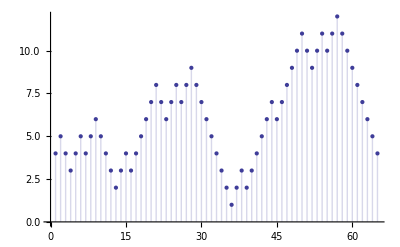

```mathematica
ListPlot[history[[All, 1,2]],Joined->False,Filling->Axis]
```

```mathematica
ArrayPlot[history[[All, 2]],ColorRules->{0->White,1->Green,2->Red,3->Blue},AspectRatio->GoldenRatio,ImageSize->500]
```

-Graphics-

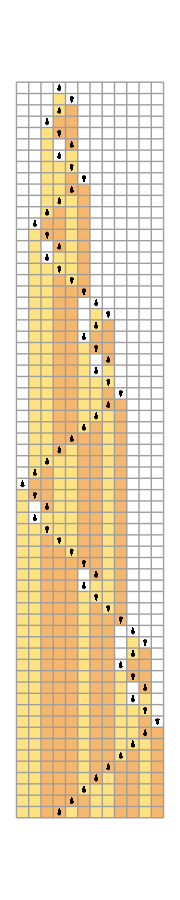
-Graphics-64 steps

```mathematica
DrawHistory[history, {2,3}]
```

## Compression of Input

### compress history by keeping only those rows in which the head moved further to the left or right than ever before

```mathematica
CompressHistory[history_] := Module[{min=0,max=0},
	compressed=Reap[
		Scan[
			Function[row,Module[{pos},
				pos =row[[1,3]];
				If[pos > max, Sow[row]; max = pos];
				If[pos < min, Sow[row]; min = pos];
			]],
			history
		]
	][[2,1]]
]
```

```mathematica
history=TuringMachine[{596440,2,3},{1,{{},0}},64];
```

### see a compressed version of the 2,3 UTM

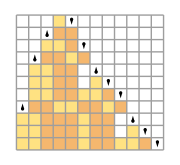
-Graphics-10 steps

```mathematica
compressed=CompressHistory[history];
DrawHistory[compressed,{2,3}]
```

### define compression ratio as the fraction of the history that remained after compression

```mathematica
CompressionRatio[rule_] := Module[
	{history,compressed},
	history = TuringMachine[rule,{1,{{},0}},128][[16;;]];
	compressed = CompressHistory[history];
	N[Length[compressed]/Length[history]]
];
```

```mathematica
CompressionRatio[{0,2,3}]
```

1.

### sample 512 random machines and sort them by their compression ratio

```mathematica
RandomSeed[1];
rand=RandomInteger[NumRules[2,3],512];
ratios=CompressionRatio[{#,2,3}]&/@rand;
order=Ordering[ratios];
ranked=rand[[order]];
```

### Use tooltips to be able to see the TM that produced a given compression ratio. Try to characterize the different ‘bands’ of compression ratio here by mousing over them.

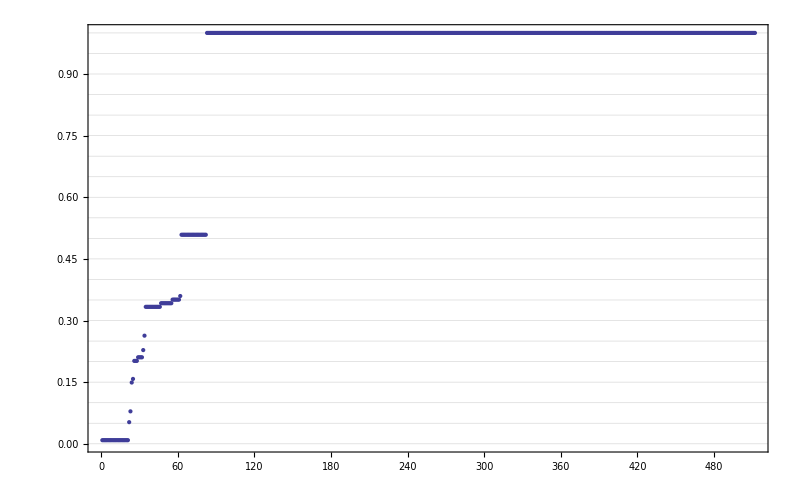

```mathematica
ListPlot[
Sort[MapThread[
Tooltip[#1,Labeled[Dynamic[DrawHistory[TuringMachine[{#2,2,3},{1,{{},0}},24],{2,3}]], #2]]&,
{ratios,rand}
]
],ImageSize->800,Frame->True,GridLines->{None,Range[0,1,.05]}]
```

### examine a rule near the bottom right in more detail

```mathematica
DrawHistory[TuringMachine[{241816,2,3}, {1, {{},0}}, 32],{2,3}]
```

-Graphics-32 steps

### It is clearly nested.

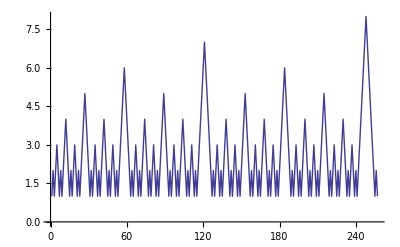

```mathematica
ListPlot[TuringMachine[{241816,2,3}, {1, {{},0}}, 256][[All,1,2]],Joined->True]
```